```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/Fluorescence"];
Table[A[i]=Cases[Import[#[[i]],"Table"],{_Real,_Real}],{i,1,Length[#]}]&@FileNames["*.TXT"];
```

```mathematica
TableForm[Transpose[{Range[Length[#]],#}]&@FileNames["*.TXT"]]
```

1 | 0_5_2ND.TXT
2 | 0_5EM2ND.TXT
3 | 0_5EMIT'.TXT
4 | 0_5EMIT.TXT
5 | 0_5'.TXT
6 | 0_5.TXT
7 | 10MLACOH.TXT
8 | 20MLACOH.TXT
9 | 5MLACOH.TXT
10 | BACK'.TXT
11 | BACK.TXT
12 | PH_MIN'.TXT
13 | PH_MIN.TXT
14 | STANDARD.TXT
15 | UNKNOWN.TXT

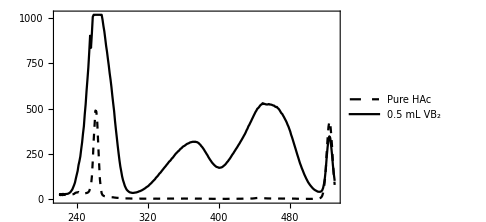

```mathematica
ListLinePlot[{A[11],A[6]},PlotRange->All,ImageSize->Medium,Frame->True,PlotStyle->{{Black,Dashed},{Black}},Axes->False,PlotLegends->{"Pure HAc","0.5 mL VB_2"}]
```

```mathematica
ListLinePlot[{A[13],A[9],A[7],A[8],A},PlotRange->All,ImageSize->Medium,Frame->True,PlotStyle->{{Black,Dashed},{Black}},Axes->False,PlotLegends->{"Pure HAc","0.5 mL VB_2"}]
```

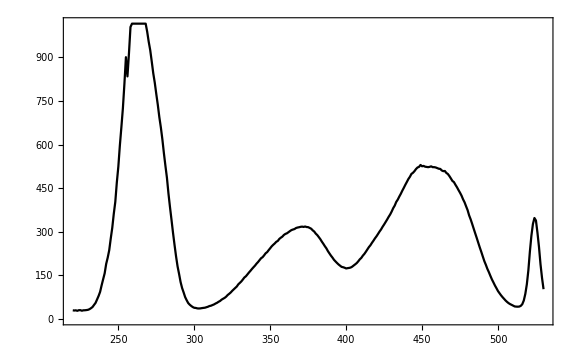

```mathematica
ListLinePlot[Cases[Import["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/Fluorescence/0_5.TXT","Table"],{_Real,_Real}],PlotRange->All,ImageSize->Large,Frame->True,Axes->False,PlotStyle->Black]
```

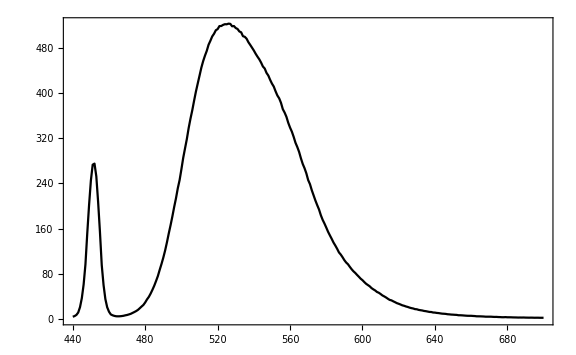

```mathematica
ListLinePlot[Cases[Import["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/Fluorescence/0_5EMIT.TXT","Table"],{_Real,_Real}],PlotRange->All,ImageSize->Large,Frame->True,Axes->False,PlotStyle->Black]
```

```mathematica
ListLinePlot[Cases[Import["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/Fluorescence/0_5EMIT.TXT","Table"],{_Real,_Real}],PlotRange->All,ImageSize->Large,Frame->True,Axes->False,PlotStyle->Black]
```

```mathematica
FileNames["*.TXT"]
```

{0_5_2ND.TXT,0_5EM2ND.TXT,0_5EMIT'.TXT,0_5EMIT.TXT,0_5'.TXT,0_5.TXT,10MLACOH.TXT,20MLACOH.TXT,5MLACOH.TXT,BACK'.TXT,BACK.TXT,PH_MIN'.TXT,PH_MIN.TXT,STANDARD.TXT,UNKNOWN.TXT}

```mathematica
"0_5_2ND.TXT"//ToBoxes
```

"0_5_2ND.TXT"

```mathematica
SetDirectory["F:\\GitHub\\Elucate\\中级化学实验报告\\data\\Chromatography"];
```

```mathematica
FileNames[]
```

{std-01.txt,std-02.txt,std-03.txt,std-04.txt,std-05.txt,std-06.txt,std-07.txt,std-08.txt,std-09.txt,std-10.txt,std-11.txt,std-12.txt}

```mathematica
Table[A[i]=Cases[Import[#[[i]],"Table"],{_Real,_Integer}],{i,1,Length[#]}]&@FileNames["*.TXT"];
```

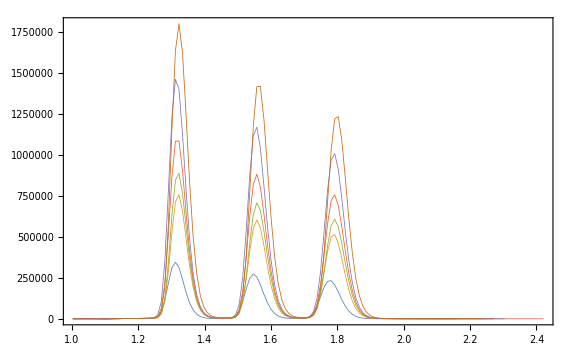

```mathematica
ListLinePlot[Select[#,#[[1]]>1&]&/@A/@Range[6],PlotRange->All,PlotStyle->Thickness[0.001],ImageSize->Large,Frame->True,Axes->False]
```

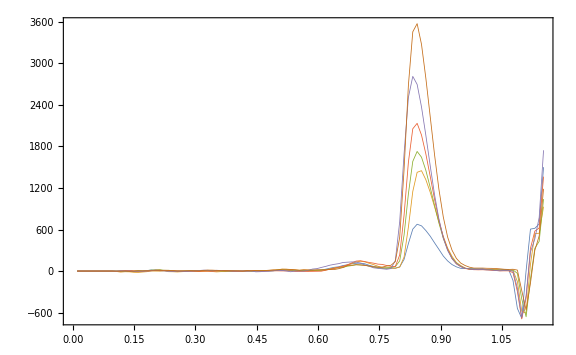

```mathematica
ListLinePlot[Select[#,0<#[[1]]<1.16&]&/@A/@Range[6],PlotRange->All,PlotStyle->Thickness[0.001],ImageSize->Large,Frame->True,Axes->False]
```

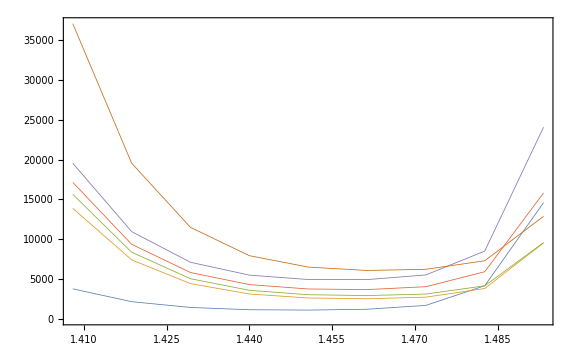

```mathematica
ListLinePlot[Select[#,1.4<#[[1]]<1.5&]&/@A/@Range[6],PlotStyle->Thickness[0.001],ImageSize->Large,Frame->True,Axes->False]
```